## Study the behavior of the oscillator frequencies ω_1 and ω_2

```mathematica
ClearAll["Global`*"]
```

```mathematica
S[I_,j_]:=(2I-1-2j)/(2I-1);
SP[I_,j_]:=(2j-2I-1)/(2j-1);
T[j_,γ_]:=1/(j(j+1))Sqrt[3](Sqrt[3]Cos[γ]+Sin[γ]);
TP[j_,γ_]:=1/(j(j+1))2Sqrt[3]Sin[γ];
```

### Create the omega sub-terms

### Nuclear total spin -> i Single-particle spin -> j

```mathematica
st1[i_,j_,a1_,a3_]:=(2i-1)(a3-a1)+2*j*a1;
st2[i_,j_,a1_,a2_]:=(2i-1)(a2-a1)+2*j*a1;
st3[i_,j_,a1_,a3_,v_,γ_]:=(2j-1)(a3-a1)+2*i*a1+v*(2j-1)/(j(j+1))Sqrt[3](Sqrt[3]Cos[γ]+Sin[γ]);
st4[i_,j_,a1_,a2_,v_,γ_]:=(2j-1)(a2-a1)+2i*a1+v*(2j-1)/(j(j+1))2Sqrt[3]*Sin[γ];
```

```mathematica
omega1[i_,j_,a1_,a2_,a3_]:=(st1[i,j,a1,a3]*st2[i,j,a1,a2])^(1/2);
omega2[i_,j_,a1_,a2_,a3_,v_,γ_]:=(st3[i,j,a1,a3,v,γ])^(1/2)*(st4[i,j,a1,a2,v,γ])^(1/2);
```

### Numerical interpretation

```mathematica
j0=13/2;
A1=0.02;
V=3;
γ=25*π/180;
Print[1/(2*A1)]
```

25.

## Create numerical data

### Omega1

```mathematica
Print[{A1,A1*S[spin,j0]}/.{spin->35/2}]
```

{0.02,0.0123529}

### Omega2

```mathematica
Print[{A1,SP[spin,j0]*A1-V*TP[j0,γ],SP[spin,j0]*A1-V*T[j0,γ]}/.{spin->35/2}]
```

{0.02,-0.128425,-0.250698}

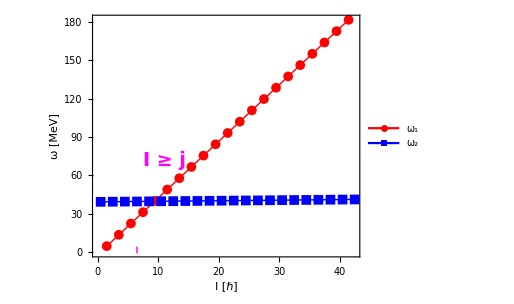

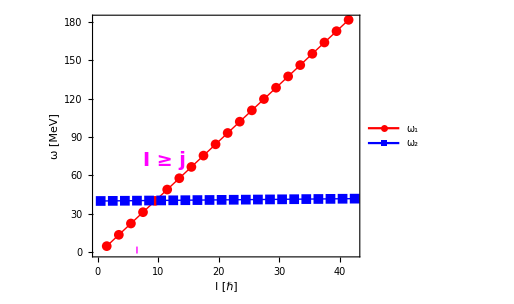

```mathematica
(*data1=Table[{i,omega1[i,j0,A1,A1+Abs[A1*S[i,j0]],2A1+Abs[A1*S[i,j0]]]},{i,3/2,85/2,2}];*)
data1=Table[{i,omega1[i,j0,A1,1,5]},{i,3/2,85/2,2}];
(*data2=Table[{i,omega2[i,j0,A1,A1+Abs[SP[i,j0]*A1-V*TP[j0,γ]],2A1+Abs[SP[i,j0]*A1-V*T[j0,γ]],V,γ]},{i,1/2,85/2,2}];*)
data2=Table[{i,omega2[i,j0,A1,2,5,V,γ]},{i,1/2,85/2,2}];
(*data3=Table[{i,omega1[i,j0,A1,2*A1+Abs[A1*S[i,j0]],A1+Abs[A1*S[i,j0]]]},{i,3/2,85/2,2}];*)
data3=Table[{i,omega1[i,j0,A1,5,1]},{i,3/2,85/2,2}];
(*data4=Table[{i,omega2[i,j0,A1,5*A1+Abs[SP[i,j0]*A1-V*TP[j0,γ]],A1+Abs[SP[i,j0]*A1-V*T[j0,γ]],V,γ]},{i,1/2,85/2,2}];*)
data4=Table[{i,omega2[i,j0,A1,5,2,V,γ]},{i,1/2,85/2,2}];
fig1=ListPlot[{data1,data2},Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,FrameStyle->Directive[Black, Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},AspectRatio->0.8,FrameLabel->{"I [ℏ]","ω [MeV]"},LabelStyle->{19,Bold,Black,FontFamily->"Arial"},PlotLegends->Placed[{"ω_1","ω_2"},{0.4,0.85}],PlotRange->{Full,Automatic},ImageSize->380,Epilog->{ Inset[Style["I ≥ j",Magenta,Bold,FontFamily->"Palatino",19],Scaled[{0.27,0.4}]]}];
fig2=ListPlot[{data3,data4},Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,FrameStyle->Directive[Black, Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},AspectRatio->0.8,FrameLabel->{"I [ℏ]","ω [MeV]"},LabelStyle->{19,Bold,Black,FontFamily->"Arial"},PlotLegends->Placed[{"ω_1","ω_2"},{0.4,0.85}],PlotRange->{Full,Automatic},ImageSize->380,Epilog->{ Inset[Style["I ≥ j",Magenta,Bold,FontFamily->"Palatino",19],Scaled[{0.27,0.4}]]}];
obg1=Show[{fig1,Graphics[{Thick,Dashed,Magenta,Line[{{j0,-1},{j0,7}}]}]}];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/wobbling-frequency-algebraic/omega-1-2-frequencies-1.pdf",obg1];
obg2=Show[{fig2,Graphics[{Thick,Dashed,Magenta,Line[{{j0,-1},{j0,7}}]}]}];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/wobbling-frequency-algebraic/omega-1-2-frequencies-2.pdf",obg2];
obg1
obg2
```

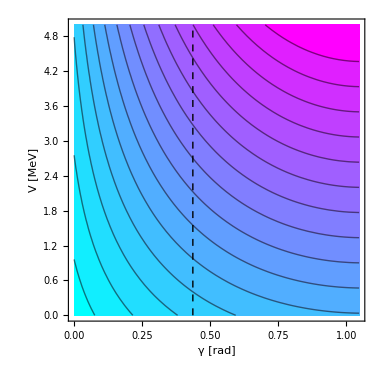

0.02

0.148425

0.290698

```mathematica
CoolColor[ z_ ] :=RGBColor[z,1-z,1];
cp=ContourPlot[omega2[35/2,j0,A1,A1+Abs[SP[35/2,j0]*A1-V*TP[j0,y]],2A1+Abs[SP[35/2,j0]*A1-V*T[j0,y]],x,y],{y,0,60π/180},{x,0,5},Contours->15(*ContourLabels->(Text[Style[#3,Red,Bold,13],{#1,#2},Background->None]&)*),ColorFunction->CoolColor,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"γ [rad]","V [MeV]"},LabelStyle->{19,Bold,Black,FontFamily->"Arial"},ImageSize->380,PlotRangePadding->0,PlotLegends->BarLegend[Automatic,LegendMarkerSize->300,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"ω_2 [MeV]"]];
obj=Show[cp,Graphics[{Black,Thick,Dashed,Line[{{25*π/180,0},{25*π/180,5}}]}]];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/wobbling-frequency-algebraic/omega-2-gamma-V.pdf",obj];
obj
A1
A1+Abs[SP[35/2,j0]*A1-V*TP[j0,25*π/180]]
2A1+Abs[SP[35/2,j0]*A1-V*T[j0,25*π/180]]
```

```mathematica
data2
```

{{1/2,39.3643},{5/2,39.4529},{9/2,39.5415},{13/2,39.63},{17/2,39.7184},{21/2,39.8069},{25/2,39.8953},{29/2,39.9836},{33/2,40.072},{37/2,40.1603},{41/2,40.2485},{45/2,40.3367},{49/2,40.4249},{53/2,40.5131},{57/2,40.6012},{61/2,40.6893},{65/2,40.7774},{69/2,40.8654},{73/2,40.9534},{77/2,41.0413},{81/2,41.1292},{85/2,41.2171}}

```mathematica
data4
```

{{1/2,40.0297},{5/2,40.1168},{9/2,40.2039},{13/2,40.2909},{17/2,40.3779},{21/2,40.4649},{25/2,40.5519},{29/2,40.6388},{33/2,40.7257},{37/2,40.8126},{41/2,40.8995},{45/2,40.9863},{49/2,41.0731},{53/2,41.1598},{57/2,41.2466},{61/2,41.3333},{65/2,41.42},{69/2,41.5066},{73/2,41.5933},{77/2,41.6799},{81/2,41.7665},{85/2,41.853}}

```mathematica
60*π/180
```

π/3